```mathematica
Import["~/faks/2_stopnja/mag_sem/magisterij/mag.m"]
$Assumptions={Element[x,Reals],h>0,a>0,y>0};
p[x_]:=b0 x^5+a0 x^4+a x^3+ b x^2 + c x+ d
sol =First@Solve[{p[0]==p0,p'[0]==0,p'[h]==0, p[h]==0,p''[h]==0,p''[0]==0},{b,c,d,a,a0,b0}];
q = p[x]/.sol // Simplify
```

(p0 (h-x)^3 (h^2+3 h x+6 x^2))/h^5

```mathematica
q/.x->r// FortranForm
```

(p0*(h - r)**3*(h**2 + 3*h*r + 6*r**2))/h**5

```mathematica
Manipulate[
Plot[
1/2 p0 (h-x)^2 (h+2 x),{x,0,h},Evaluate[pltopts]
],{{p0,1},0,5},{{h,1},0.001,10}]
```

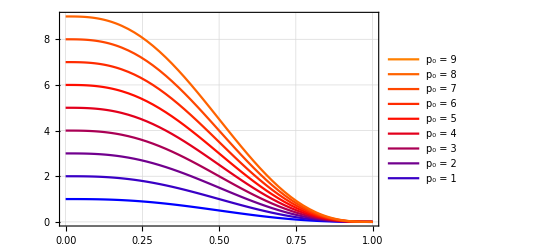

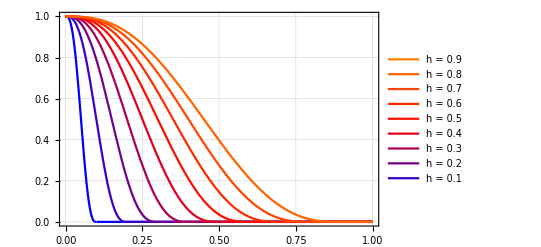

```mathematica
Clear[spl]
spl[x_,h_,p0_:p0]:=Piecewise[{{(p0 (h-x)^3 (h^2+3 h x+6 x^2))/h^5,x<h},{0,True}}]
Qlist=Range[1,9];
leglist=Table["p_0 = "<>ToString[x],{x,Qlist}];
cols=Table[Blend[{Blue, Red, Orange},x],{x,0,1,1/Length@Qlist}];
Qplots=FPlot[
Evaluate@Table[
spl[x,1]/.{p0->Q0},{Q0,Qlist}]
,{x,0,1},
PlotLegends->LineLegend[Reverse[cols],Reverse[leglist]],
PlotStyle->cols
]
hlist = Range[0.1,0.9,0.1];
leglist=Table["h = "<>ToString[x],{x,hlist}];
cols=Table[Blend[{Blue, Red, Orange},x],{x,0,1,1/Length@hlist}];
hplots = FPlot[
Evaluate@Table[
spl[x,h]/.{p0->1},{h,hlist}]
,{x,0,1},
PlotLegends->LineLegend[Reverse[cols],Reverse[leglist]],
PlotStyle->cols,
PlotRange->All
]
```

```mathematica
L=Laplacian[spl[r,h],{r,phi},"Polar"]//Simplify
center = {1/2,1-1/10};
L = L/.{r->EuclideanDistance[{x,y},center]};
```

Piecewise[{{-(30 p0 r (3 h^2-8 h r+5 r^2))/h^5, h>r}, {0, True}}]

```mathematica
-(30 p0 r (3 h^2-8 h r+5 r^2))/h^5//InputForm
```

(-30*p0*r*(3*h^2 - 8*h*r + 5*r^2))/h^5

```mathematica
spl[r,h]//ToMatlab
```

ToMatlab[Piecewise[{{(p0 (h-r)^3 (h^2+3 h r+6 r^2))/h^5, r<h}, {0, True}}]]

```mathematica
H = spl[EuclideanDistance[{x,y},center],1/10,1]// FullSimplify;
Plot3D[H,{x,0,1},{y,0,1},PlotRange->All,Exclusions->None]
Plot3D[L/.{h->1/10,p0->1},{x,0,1},{y,0,1},PlotRange->All,Exclusions->None]
```

-Graphics3D-

-Graphics3D-

```mathematica
usoln=NDSolveValue[{Laplacian[u[x,y],{x,y}]==L/.{h->1/10,p0->1},u[x,0]==0,u[0,y]==0,u[1,y]==0,u[x,1]==0},u,{x,0,1},{y,0,1}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
Plot3D[usoln[x,y],{x,0,1},{y,0,1},PlotRange->All]
```

-Graphics3D-